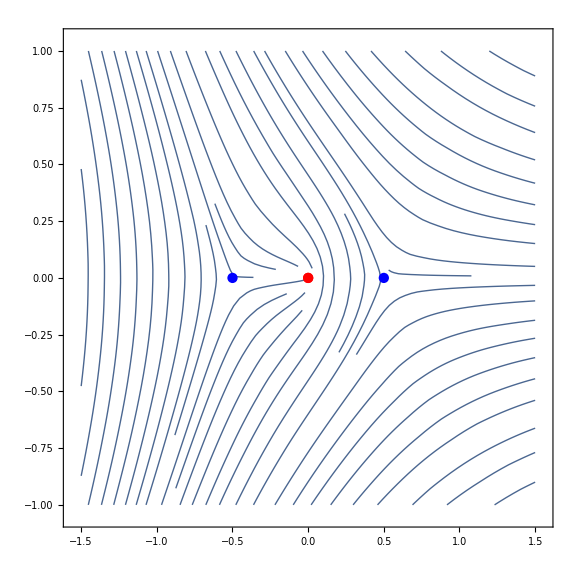
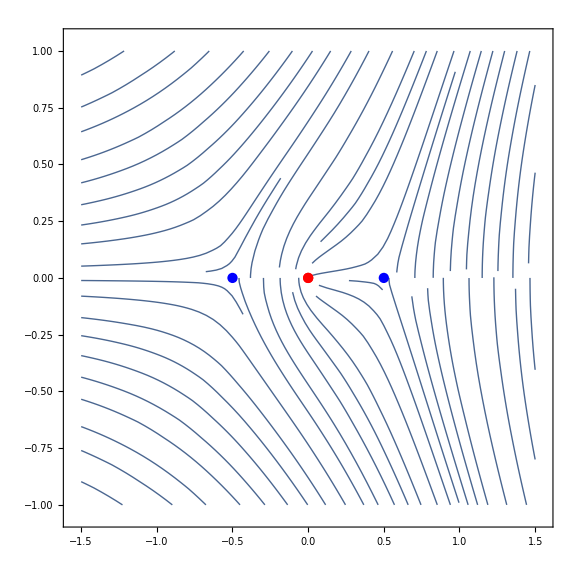

```mathematica
β=0.5;
potential=Function[x,-x+β^2/x];
StokesGraph[potential,1]
Clear[β,potential];
```

```mathematica
F=({{ⅇ^i, 0}, {r ⅇ^i, ⅇ^-i}});(*r->b+aⅇ^(-2i),F=S[b].W[i].S[a]*)
P=S[ⅈ p]ᵀ;
F.{1,0};
%⟦2⟧/%⟦1⟧//Simplify
F*.P.{1,0};
%⟦1⟧/%⟦2⟧//Simplify
```

r

1/Conjugate[r]

```mathematica
Inverse[J.F*.J]*.F*.P.{1,0};
(J.P*.J).Inverse[J.F*.J].F.{1,0}/.p*->p;
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦1⟧ⅇ^(4/3 ρ^(3/2))+%%⟦2⟧), 1, (Log[ρ]+2π ⅈ)}, {ⅈ(%⟦1⟧ⅇ^(4/3 ρ^(3/2))+%⟦2⟧), 1, (Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
D[%,ρ]/(2 √ρ)ⅇ^(-4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(4/3 ρ^(3/2))//Simplify

Inverse[J.F*.J]*.F*.P.{0,1};
(J.P*.J).Inverse[J.F*.J].F.{0,1}/.p*->p;
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦1⟧+%%⟦2⟧ⅇ^(-4/3 ρ^(3/2))), 1, (Log[ρ]+2π ⅈ)}, {ⅈ(%⟦1⟧+%⟦2⟧ⅇ^(-4/3 ρ^(3/2))), 1, (Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
-D[%,ρ]/(2 √ρ)ⅇ^(4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(-4/3 ρ^(3/2))//Simplify
```

0

2 π (-2 ⅈ+ⅈ ⅇ^(i+Conjugate[i]) p-ⅇ^(i-Conjugate[i]) r+ⅇ^(-i+Conjugate[i]) (1-ⅈ ⅇ^(2 i) p r) Conjugate[r])

0

2 π (-2 ⅈ+ⅈ ⅇ^(i+Conjugate[i]) p-ⅇ^(i-Conjugate[i]) r+ⅇ^(-i+Conjugate[i]) (1-ⅈ ⅇ^(2 i) p r) Conjugate[r])

```mathematica
ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i])/p +(2 ⅇ^(-2 Re[i])/p -1)==0;
Solve[ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i])/p +(2 ⅇ^(-2 Re[i])/p -1)==0,ρ]
```

{{ρ→1/2 (-(2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]])/p-√(4-(8 ⅇ^(-2 Re[i]))/p+(4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2)/p^2))},{ρ→1/2 (-(2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]])/p+√(4-(8 ⅇ^(-2 Re[i]))/p+(4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2)/p^2))}}

```mathematica
Integrate[ⅈ √((1-x^2)/x)ⅈ x/.x->ⅇ^(ⅈ ϕ),{ϕ,0,-π}]
```

((1-ⅈ) √π Gamma[5/4])/Gamma[7/4]

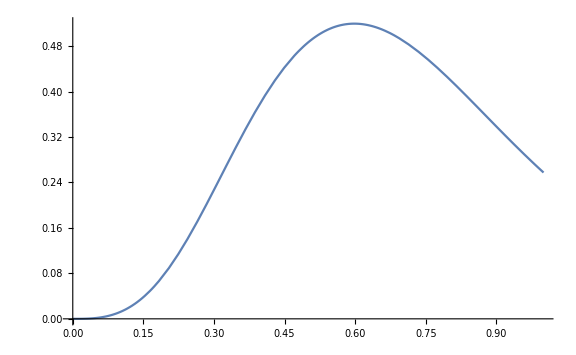

```mathematica
Plot[1-ρ^2/.ρ->(ⅇ^(-2 Re[i]) (-2 Cosh[2 Im[i]]+√2 √(1-4 ⅇ^(2 Re[i]) p+2 ⅇ^(4 Re[i]) p^2+Cosh[4 Im[i]])))/(2 p)/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2)/.p->2/3 ⅇ^(β^(3/2))(1-ⅇ^(β^(3/2))),{β,0,1},PlotRange->Full,ImageSize->Large]
```

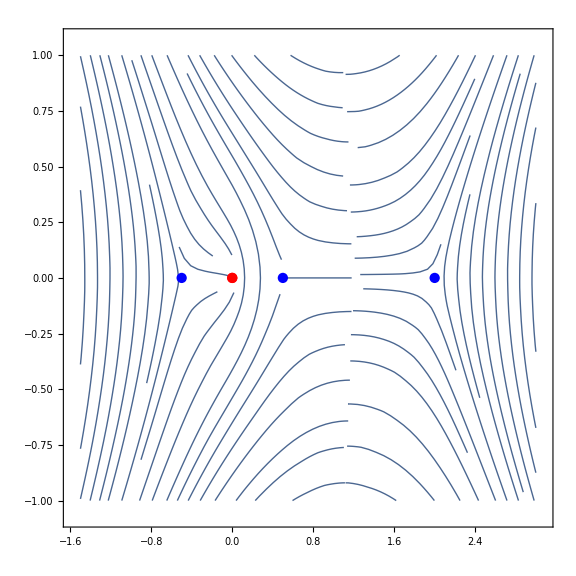
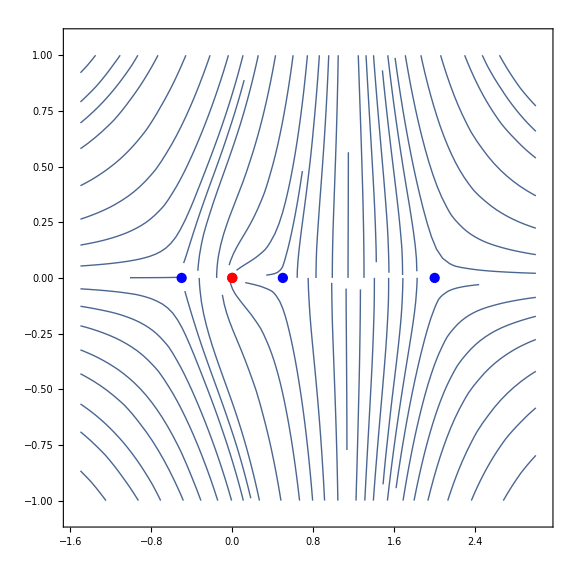

```mathematica
β=0.5;l=2;
potential=Function[x,(β^2-x^2)/x(1-x/l)];
StokesGraph[potential,1]
Clear[β,l,potential];
```

```mathematica
S[b]ᵀ.W[-i].S[a]ᵀ.W[-L].S[c]//Simplify//MatrixForm
```

(ⅇ^(-i-L)+a c ⅇ^(-i+L)+b c ⅇ^(i+L) | ⅇ^(-i+L) (a+b ⅇ^(2 i))
c ⅇ^(i+L) | ⅇ^(i+L))

```mathematica
F=({{ⅇ^(-i-L)+c r ⅇ^(i+L), r ⅇ^(i+L)}, {c ⅇ^(i+L), ⅇ^(i+L)}});(*r->b+aⅇ^(-2i),c->-ⅈ,F=S[b]ᵀ.W[-i].S[a]ᵀ.W[-L].S[с]*)
F.{1,0};
1-Abs[%⟦1⟧/%⟦2⟧]^2-Abs[1/%⟦2⟧]^2//Simplify
J.F*.J.{1,0};
1-Abs[%⟦1⟧/%⟦2⟧]^2-Abs[1/%⟦2⟧]^2//Simplify
```

1-ⅇ^(-2 Re[i+L])/Abs[c]^2-ⅇ^(-2 Re[i+L]) Abs[ⅇ^(-i-L)/c+ⅇ^(i+L) r]^2

-(1+ⅇ^(-2 Re[i+L])-Abs[r]^2)/Abs[r]^2

```mathematica
Limit[ⅇ^(-2 Re[i+L]) (-1+ⅇ^(2 Re[i+L])-Abs[ⅇ^(-i-L)-ⅈ ⅇ^(i+L) r]^2),L->Infinity]
Limit[-(1+ⅇ^(-2 Re[i+L])-Abs[r]^2)/Abs[r]^2,L->Infinity]
```

1-Im[r]^2-Re[r]^2

1-1/Abs[r]^2

```mathematica
Inverse[F].(J.F*.J).{1,0}/.(i+L)*->(i*+L)/.L*->L//Simplify//MatrixForm
```

```mathematica
({{ⅇ^(2Re[i]+2 L) a}, {-a c ⅇ^(2Re[i]+2L) +Conjugate[r] ⅇ^(-2ⅈ Im[i])}})
```

```mathematica
Inverse[J.F*.J].F.{1,0}/.(i+L)*->(i*+L)/.L*->L//Simplify//MatrixForm
```

```mathematica
({{-(ⅇ^(2Re[i]+L) Abs[c]^2 a-ⅇ^(-2Re[i]-2L)-c*r*ⅇ^(-2ⅈ Im[i])-c r ⅇ^(2ⅈ Im[i]))}, {c ⅇ^(2 Re[i]+2L)a-Conjugate[r] ⅇ^(-2ⅈ Im[i])}})
```

```mathematica
({{ⅇ^(2Re[i]+2 L) a}, {-a c ⅇ^(2Re[i]+2L) +Conjugate[r] ⅇ^(-2ⅈ Im[i])}});
({{-(ⅇ^(2Re[i]+2L) Abs[c]^2 a-ⅇ^(-2Re[i]-2L)-c*r*ⅇ^(-2ⅈ Im[i])-c r ⅇ^(2ⅈ Im[i]))}, {c ⅇ^(2 Re[i]+2L)a-Conjugate[r] ⅇ^(-2ⅈ Im[i])}});
({{1, 1, Log[ρ]}, {-(%%⟦1⟧+%%⟦2⟧ⅇ^(-ⅈ 2 ρ^2)), 1, (Log[ρ]+2π ⅈ)}, {-(%⟦1⟧+%⟦2⟧ⅇ^(-ⅈ 2 ρ^2)), 1, (Log[ρ]-2π ⅈ)}})/.(i+L)*->(i*+L)/.L*->L//Det//Simplify//Apart;
D[%,ρ]/(-4ⅈ ρ)ⅇ^(ⅈ 2 ρ^2)//Simplify
%%-%ⅇ^(-ⅈ 2 ρ^2)//Simplify
```

0

-2 ⅈ π (2+ⅇ^(-2 (L+Re[i]))+a ⅇ^(2 (L+Re[i]))+c ⅇ^(2 ⅈ Im[i]) r-a ⅇ^(2 (L+Re[i])) Abs[c]^2+ⅇ^(-2 ⅈ Im[i]) Conjugate[c] Conjugate[r])

```mathematica
2+ⅇ^(-2 Re[i]-2L)+a ⅇ^(2Re[i]+2 L)(1-Abs[c]^2)+c r ⅇ^(2 ⅈ Im[i])+c*r*ⅇ^(-2 ⅈ Im[i])
Abs[r]^2+2Im[r ⅇ^(2ⅈ Im[i])] ⅇ^(-2Re[i])+(2 ⅇ^(-2Re[i])-1)==0
```

```mathematica
Solve[ρ^2+2ρ Sin[2Im[i]+ ϕ] ⅇ^(-2Re[i])+(2 ⅇ^(-2Re[i])-1)==0,ρ]
```

{{ρ→1/2 (-2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]]-√(4-8 ⅇ^(-2 Re[i])+4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2))},{ρ→1/2 (-2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]]+√(4-8 ⅇ^(-2 Re[i])+4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2))}}

```mathematica
ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i])/p +(2 ⅇ^(-2 Re[i])/p -1)==0;
ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i]) +(2 ⅇ^(-2 Re[i]) -1)==0;
```

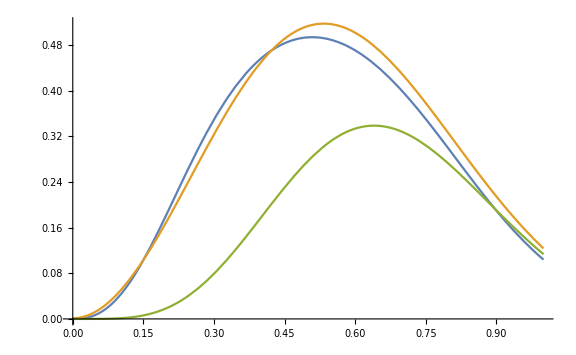

```mathematica
Plot[{2 ⅇ^(-2Re[i])((1-s^2 ⅇ^(-2Re[i]))+s √(1-ⅇ^(-2Re[i])(2-s^2 ⅇ^(-2Re[i]))))/.s->(*(-(2-m dissFunc[β] ⅇ^(2 Re[i]))/(2 √(1- m dissFunc[β])))/.m->0.895*)Sin[ϕ+2Im[i]]/.ϕ->-π/2+7 β^2-π β^3-2Im[i]/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2),dissFunc[β],4 ⅇ^-δ(1-ⅇ^-δ)Sin[δ/2]^2/.δ->3.5 β^(3/2)},{β,0,1},PlotRange->Full,ImageSize->Large]
```

```mathematica
Plot3D[1-ⅇ^(-2Re[i])(2-s^2 ⅇ^(-2Re[i]))/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2),{s,-1,1},{β,0,1}]
```

-Graphics3D-

```mathematica
dissFunc=Interpolation[βDissipation];
```

```mathematica
Solve[2 ⅇ^(-2Re[i])((1-s^2 ⅇ^(-2Re[i]))+s √(1-ⅇ^(-2Re[i])(2-s^2 ⅇ^(-2Re[i]))))==a,s]
```

{{s→-(ⅈ (-2+a ⅇ^(2 Re[i])))/(√(-4+4 a))},{s→(ⅈ (-2+a ⅇ^(2 Re[i])))/(√(-4+4 a))}}

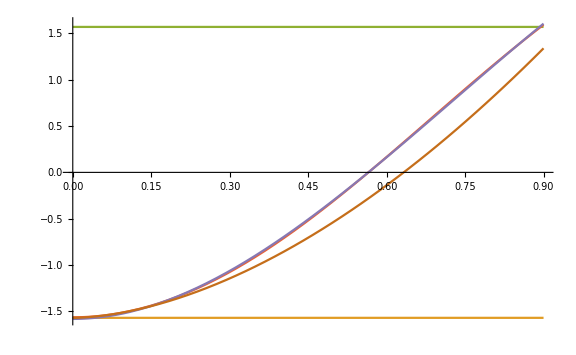

```mathematica
Plot[{ArcSin[(-(2-a ⅇ^(2 Re[i]))/(2 √(1- a)))]/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2)/.a->(*4 ⅇ^-δ(1-Sin[δ/2]^2 ⅇ^-δ)Sin[δ/2]^2/.δ->3.5 β^(3/2)*)0.8952dissFunc[β],-π/2,π/2,0.571351375804772-2.1362777792258747 Cos[2.3`2. β],-1.5824726408686782+6.674239183762206 β^2-3.041924811453713 β^3,Arg[-ⅈ ⅇ^(ⅈ 3.5 β^(7/4))]},{β,0,0.9},PlotRange->All,ImageSize->Large]
```

```mathematica
{{"0.00124","-1.565"},{"0.01488","-1.565"},{"0.03223","-1.565"},{"0.05206","-1.552"},{"0.06818","-1.545"},{"0.08801","-1.525"},{"0.1066","-1.498"},{"0.1277","-1.471"},{"0.1488","-1.437"},{"0.1673","-1.404"},{"0.1847","-1.377"},{"0.2058","-1.33"},{"0.2244","-1.283"},{"0.2467","-1.236"},{"0.2665","-1.182"},{"0.2876","-1.121"},{"0.3074","-1.061"},{"0.3297","-0.9869"},{"0.3508","-0.913"},{"0.3731","-0.8323"},{"0.3954","-0.7449"},{"0.4153","-0.6643"},{"0.4339","-0.5836"},{"0.4525","-0.503"},{"0.4735","-0.4156"},{"0.4909","-0.3349"},{"0.5107","-0.2476"},{"0.5293","-0.1535"},{"0.5467","-0.07952"},{"0.5677","0.02802"},{"0.5888","0.1288"},{"0.6136","0.2364"},{"0.6409","0.3708"},{"0.6607","0.4784"},{"0.693","0.6262"},{"0.7202","0.7539"},{"0.7475","0.8816"},{"0.7748","1.009"},{"0.8045","1.15"},{"0.8281","1.258"},{"0.8529","1.379"},{"0.8739","1.473"},{"0.8863","1.534"}}//ToExpression;
FindFormula[%,β,TargetFunctions->{Times,Exp,Plus}]
```

-1.58247+6.67424 β^2-3.04192 β^3

```mathematica
AiryR=GetR[-(x-ⅈ 10^-5),ⅈ √(x-ⅈ 10^-5),{x,10,-100},0];
```

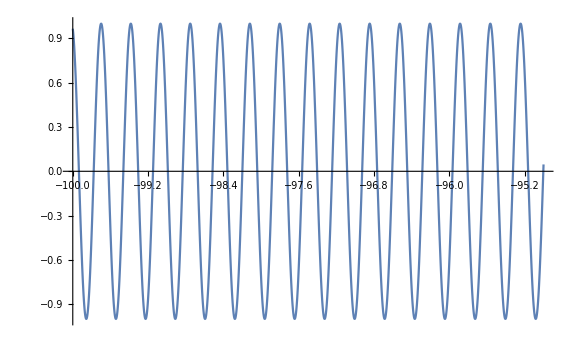

```mathematica
Plot[Re[AiryR[x]],{x,-100,-95},ImageSize->Large]
```

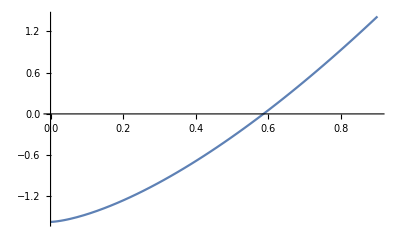

```mathematica
Plot[Arg[-ⅈ ⅇ^(ⅈ 3.5 b^(3/2))],{b,0,0.9}]
```

```mathematica
GetR[extQ_,extk_,intvl_,init_]:=
Module[{Q,k,M,U,r,x,externalSymbol,localVar,a,b},
externalSymbol=Unevaluated[intvl]/.{x_,y__}:>HoldPattern[x];
Q=Unevaluated[extQ]/.externalSymbol:>localVar;
k=Unevaluated[extk]/.externalSymbol:>localVar;
{a,b}=Rest[intvl];

U=({{1, 1}, {ⅈ k-1/(2k), -ⅈ k-1/(2k)}});
M=Inverse[U].(({{0, 1}, {-Q, 0}}).U-D[U,localVar]);
r=NDSolveValue[{D[x[localVar],localVar]==-(M⟦1,2⟧x[localVar]^2+(M⟦1,1⟧-M⟦2,2⟧)x[localVar]-M⟦2,1⟧),x[a]==init},x,{localVar,a,b},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->20,MaxSteps->Infinity];
r
];
```

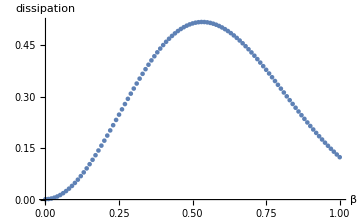

```mathematica
(*TEM dissipation for X-wave*)
βDissipation={};
α=10^-4;l=10;
βbegining=0;βend=1;βnstep=100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β≤βend,β+=(βend-βbegining)/βnstep,
r=GetR[(β^2-z^2)/z/.{z->z-ⅈ α},ⅈ √(z-ⅈ α),{z,l,-l},0];
βDissipation=Append[βDissipation,{β,1-Abs[r[-l]]^2}];
];
ListPlot[βDissipation,PlotRange->Full,AxesLabel->{"β","dissipation"},ImageSize->Medium]
(*SaveData[config["isotropism","data"],δDissipation]*)
Clear[α,l,β,βbegining,βend,βnstep,r];
```

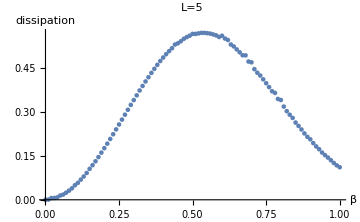

```mathematica
βDissipation={};
α=10^-5;a=20;b=-20;L=5;
βbegining=0;βend=1;βnstep=100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β≤βend,β+=(βend-βbegining)/βnstep,
r=GetR[(β^2-z^2)/z(1-z/L)/.{z->z-ⅈ α},(z-ⅈ α)/(√L),{z,a,b},0];
βDissipation=Append[βDissipation,{β,1-1/Abs[r[b]]^2}];
];
ListPlot[βDissipation,PlotRange->Full,AxesLabel->{"β","dissipation"},PlotLabel->"L="<>ToString[L],ImageSize->Medium]
(*SaveData[config["isotropism","data"],δDissipation]*)
Clear[α,a,b,L,β,βbegining,βend,βnstep,r];
```

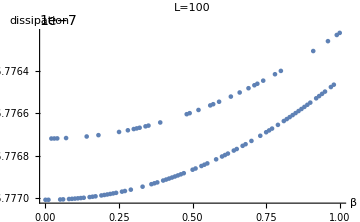

```mathematica
βDissipation={};
α=10^-5;a=110;b=90;L=100;
βbegining=0;βend=1;βnstep=100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β≤βend,β+=(βend-βbegining)/βnstep,
r=GetR[(β^2-z^2)/z(1-z/L)/.{z->z-ⅈ α},(z-ⅈ α)/(√L),{z,a,b},0];
βDissipation=Append[βDissipation,{β,1-Abs[r[b]]^2}];
];
ListPlot[βDissipation,PlotRange->Full,AxesLabel->{"β","dissipation"},PlotLabel->"L="<>ToString[L],ImageSize->Medium,PlotRange->Full]
(*SaveData[config["isotropism","data"],δDissipation]*)
Clear[α,a,b,L,β,βbegining,βend,βnstep,r];
```

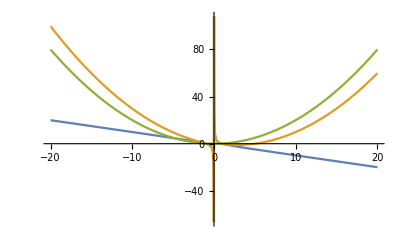

```mathematica
β=1;L=5;
Plot[{(β^2-z^2)/z,(β^2-z^2)/z(1-z/L),z^2/L},{z,-20,20}]
Clear[β,L];
```